```mathematica
(* write a basis - done *)
(* calculate hamiltonian matrix - done *)
(* get Heisenberg GS *)
(* diagonalise *)
(* calculate greens function *)

(* I consider only 1D chain with even number of sites and pbc *)
(* A hole is created in a site with a spin down *)
```

```mathematica
(* Input parameters *)
nSpinsUp=6; 
t=1.0;
J=0.4t;
beta = 1.0;
```

```mathematica
(* Helper Functions *)
getIndex[perm_]:=(
dp=Length[perm];
Sum[(d=Sum[perm[[k]],{k,s,dp}];perm[[s]]Binomial[dp-s,d]),{s,1,dp}]+1
)
```

```mathematica
(* Heisenberg Hamiltonian matrix 'Hs' calculation *)
nSites=2nSpinsUp;
nSpinsDown=nSites-nSpinsUp;
spins=Permutations[Flatten[{Table[0,nSpinsDown],Table[1,nSpinsUp]}]];
dim =Length[spins];
Hs=SparseArray[{1,1}->0,{dim,dim},0];
For[i=1,i≤dim,i++,(
spinIn=spins[[i]];
For[s1=1,s1≤nSites,s1++,(
s2=Mod[s1+1,nSites,1];
If[spinIn[[s1]]==spinIn[[s2]],
Hs[[i,i]]+=J(1 /4 - spinIn[[s1]]/2-spinIn[[s2]]/2+beta*spinIn[[s1]]*spinIn[[s2]]),(
Hs[[i,i]]+=J(1 /4 - spinIn[[s1]]/2-spinIn[[s2]]/2+beta*spinIn[[s1]]*spinIn[[s2]]);
spinOut=spinIn;
spinOut[[s1]]=spinIn[[s2]];
spinOut[[s2]]=spinIn[[s1]];
j=getIndex[spinOut];
Hs[[i,j]]+=J/2;
)];
)];
)];
Hs
ArrayPlot[Hs]
```

SparseArray[…]

-Graphics-

```mathematica
{ene,vec}=Eigensystem[Hs];
GS=vec[[Ordering[ene][[1]]]];
E0=Min[ene]; (* Heisenberg GS energy *)
```

Eigensystem::arh: Because finding 924 out of the 924 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
(* t-J Hamiltonian matrix 'H' calculation *)
nSites=2nSpinsUp;
nSpinsDown=nSites-nSpinsUp-1;
spins=Permutations[Flatten[{Table[0,nSpinsDown],Table[1,nSpinsUp]}]];
nPerms=Length[spins];
dim=nSites nPerms;
H=SparseArray[{1,1}->0,{dim,dim},0];
For[i=1,i≤dim,i++,(
H[[i,i]]=-E0-J; (* setting the energy lvl *)
holeIn=Ceiling[i/nPerms];
is=Mod[i,nPerms,1];
spinIn=spins[[is]];

(* hopping *)
holeOut=Mod[holeIn-1,nSites,1]; (* hole jumps to the left *)
spinOut=RotateRight[spinIn]; (* spins shift to the right *)
j=getIndex[spinOut]+(holeOut-1) nPerms;
H[[i,j]]=-t;

holeOut=Mod[holeIn+1,nSites,1]; (* hole jumps to the right *)
spinOut=RotateLeft[spinIn]; (* spins shift to the left *)
j=getIndex[spinOut]+(holeOut-1) nPerms;
H[[i,j]]=-t;

(* spins *)
For[s1=1;s2=s1+1,s2<nSites,s1++;s2++,(
If[spinIn[[s1]]==spinIn[[s2]],
H[[i,i]]+=J /4,(
H[[i,i]]-=J/4;
spinOut=spinIn;
spinOut[[s1]]=spinIn[[s2]];
spinOut[[s2]]=spinIn[[s1]];
j=getIndex[spinOut]+(holeIn-1) nPerms;
H[[i,j]]+=J/2;
)];
)];
)];
H
ArrayPlot[H]
```

SparseArray[…]

-Graphics-

```mathematica
{ene,vec}=Eigensystem[H]; (* Diagonalisation of t-J Hamiltonian *)
```

Eigensystem::arh: Because finding 5544 out of the 5544 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
(* Lanczos for GF clculation *)
```

```mathematica
(* creating a hole with spin 'k' in [0, 2π] *)
createHole[k_]:=(
nSpinsDown=nSites-nSpinsUp;
spins=Permutations[Flatten[{Table[0,nSpinsDown],Table[1,nSpinsUp]}]];
initState={};
For[site=1,site≤nSites,site++,(
r=site-1;
spinOrder=Ordering[spins][[1;;nPerms]];
AppendTo[initState,Exp[I k r]GS[[spinOrder]]];
spins=Map[RotateRight,spins];
)];
Flatten[initState])
```

```mathematica
iδ=0.02 I;
nMax=200;
ωPoints=501;
kPoints=nSites+1;
k=Table[2 Pi ik/(kPoints-1),{ik,0,kPoints}];
ω=Table[12.0 it/ωPoints-4,{it,0,ωPoints-1}];
A=Table[0,{j,1,ωPoints},{i,1,kPoints}];
For[ik=1,ik≤kPoints,ik++,(
state=createHole[k[[ik]]];
g=Abs[vec.state]^2;
order=Ordering[g,-Min[dim,nMax]];
gShort=g[[order]];
eneShort=ene[[order]];
For[it=1,it≤ωPoints,it++,(
A[[it,ik]]=Im[Total[gShort/(eneShort-ω[[it]]-iδ)/Pi]];
)];
Print["Minimal numerator: " ,gShort[[1]]]
)];
```

Minimal numerator: 1.01232×10^-28

Minimal numerator: 1.28429×10^-7

Minimal numerator: 2.18353×10^-7

Minimal numerator: 1.01051×10^-7

Minimal numerator: 2.08676×10^-7

Minimal numerator: 1.33071×10^-8

Minimal numerator: 3.59425×10^-29

Minimal numerator: 1.33071×10^-8

Minimal numerator: 2.08676×10^-7

Minimal numerator: 1.01051×10^-7

Minimal numerator: 2.18353×10^-7

Minimal numerator: 1.28429×10^-7

Minimal numerator: 1.01232×10^-28

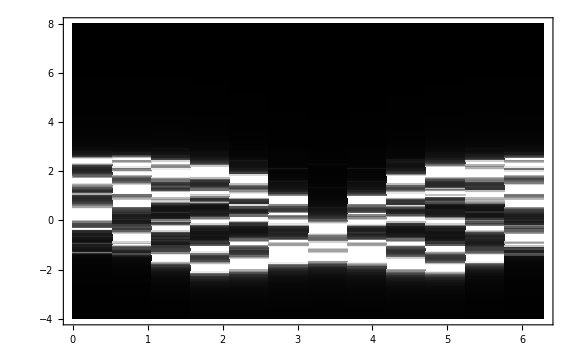

```mathematica
ListDensityPlot[A,DataRange->{{0,2Pi},{-4,8}},ColorFunction->GrayLevel,AspectRatio->1/GoldenRatio,ImageSize->Large,InterpolationOrder->0]
```

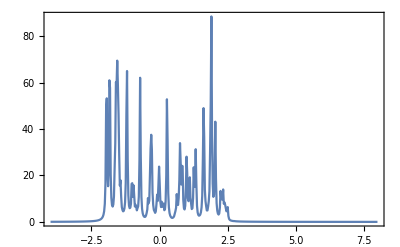

```mathematica
ListPlot[Sum[A[[;;,it]],{it,1,nSites}],PlotRange->All,DataRange->{-4,8},Axes->False,Frame->True,Joined->True] (* Plot for hole doped to site 'i' real space anihilated in the same site 'i' *)
```

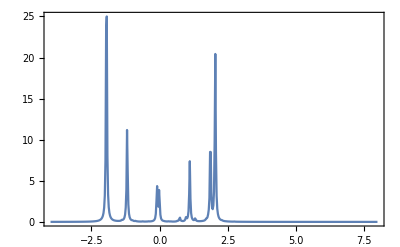

```mathematica
ListPlot[A[[;;,4]],PlotRange->All,DataRange->{-4,8},Axes->False,Frame->True,Joined->True]
```